# Algoritmo di Simulated Annealing

```mathematica
(*Obiettivo: quando l'algoritmo di Metropolis diventa inefficace (cioè al crescere del numero delle città), sfruttiamo l'algoritmo di simulated annealing. Partendo da temperature alte (cioè beta basse), all'inizio, la percentuale di accettazione è molto elevata, e sondiamo estensivamente lo spazio delle configurazioni. Abbassando la temperatura (alzando beta), diminuisce la percentuale di accettazione,e mi stabilizzo intorno al minimo, per poi convergervi (auspicabilmente).*)
```

Percorso iniziale:

Rome, Barcelona, Berlin, Athens, Belgrade

Distanza iniziale(km): 4972.73

{1,1,1,2,Distanza ottimale(km):,4902.42}

{2,1,1,5,Distanza ottimale(km):,4554.36}

{3,1,1,7,Distanza ottimale(km):,4172.97}

General::munfl: Exp[-721.463] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Percorso finale:

Rome, Barcelona, Berlin, Belgrade, Athens

Distanza finale: 4172.97

{4902.42,4554.36,4172.97}

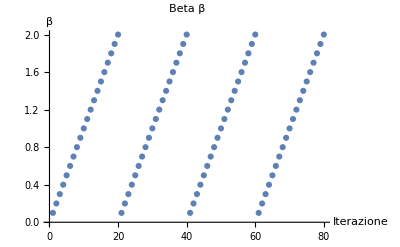

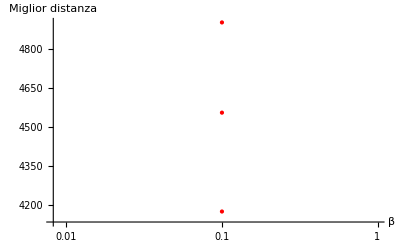

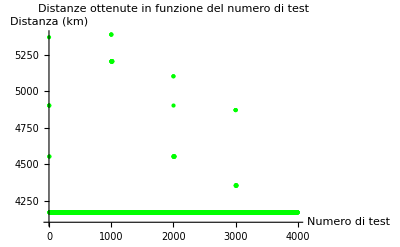

-Graphics-

"

General::munfl: Exp[-855.569] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-763.96] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.035] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
n=20;(*numero di città*)

(*Città utilizzate per l'algoritmo*)
città={<|"nome"->"Amsterdam","lat"->52.3676,"long"->4.9041|>,<|"nome"->"Athens","lat"->37.9838,"long"->23.7275|>,<|"nome"->"Barcelona","lat"->41.3851,"long"->2.1734|>,<|"nome"->"Belgrade","lat"->44.7866,"long"->20.4489|>,<|"nome"->"Berlin","lat"->52.5200,"long"->13.4050|>,<|"nome"->"Bern","lat"->46.9481,"long"->7.4474|>,<|"nome"->"Bratislava","lat"->48.1486,"long"->17.1077|>,<|"nome"->"Brussels","lat"->50.8503,"long"->4.3517|>,<|"nome"->"Bucharest","lat"->44.4268,"long"->26.1025|>,<|"nome"->"Budapest","lat"->47.4979,"long"->19.0402|>,<|"nome"->"Copenhagen","lat"->55.6761,"long"->12.5683|>,<|"nome"->"Dublin","lat"->53.3498,"long"->-6.2603|>,<|"nome"->"Edinburgh","lat"->55.9533,"long"->-3.1883|>,<|"nome"->"Frankfurt","lat"->50.1109,"long"->8.6821|>,<|"nome"->"Geneva","lat"->46.2044,"long"->6.1432|>,<|"nome"->"Helsinki","lat"->60.1695,"long"->24.9354|>,<|"nome"->"Istanbul","lat"->41.0082,"long"->28.9784|>,<|"nome"->"Kiev","lat"->50.4501,"long"->30.5234|>,<|"nome"->"Lisbon","lat"->38.7223,"long"->-9.1393|>,<|"nome"->"Ljubljana","lat"->46.0569,"long"->14.5058|>,<|"nome"->"London","lat"->51.5074,"long"->-0.1278|>,<|"nome"->"Luxembourg","lat"->49.6116,"long"->6.1319|>,<|"nome"->"Madrid","lat"->40.4168,"long"->-3.7038|>,<|"nome"->"Milan","lat"->45.4642,"long"->9.1900|>,<|"nome"->"Monaco","lat"->43.7384,"long"->7.4246|>,<|"nome"->"Moscow","lat"->55.7558,"long"->37.6173|>,<|"nome"->"Munich","lat"->48.1351,"long"->11.5820|>,<|"nome"->"Oslo","lat"->59.9139,"long"->10.7522|>,<|"nome"->"Paris","lat"->48.8566,"long"->2.3522|>,<|"nome"->"Prague","lat"->50.0755,"long"->14.4378|>,<|"nome"->"Reykjavik","lat"->64.1355,"long"->-21.8954|>,<|"nome"->"Riga","lat"->56.9496,"long"->24.1052|>,<|"nome"->"Sarajevo","lat"->43.8563,"long"->18.4131|>,<|"nome"->"Sofia","lat"->42.6977,"long"->23.3219|>,<|"nome"->"Stockholm","lat"->59.3293,"long"->18.0686|>,<|"nome"->"Tallinn","lat"->59.4370,"long"->24.7535|>,<|"nome"->"Tirana","lat"->41.3275,"long"->19.8189|>,<|"nome"->"Valletta","lat"->35.8989,"long"->14.5146|>,<|"nome"->"Vienna","lat"->48.2082,"long"->16.3738|>,<|"nome"->"Vilnius","lat"->54.6872,"long"->25.2797|>,<|"nome"->"Warsaw","lat"->52.2297,"long"->21.0122|>,<|"nome"->"Zagreb","lat"->45.8150,"long"->15.9819|>,<|"nome"->"Zurich","lat"->47.3769,"long"->8.5417|>,<|"nome"->"Seville","lat"->37.3891,"long"->-5.9845|>,<|"nome"->"Naples","lat"->40.8522,"long"->14.2681|>,<|"nome"->"Lyon","lat"->45.7640,"long"->4.8357|>,<|"nome"->"Porto","lat"->41.1579,"long"->-8.6291|>,<|"nome"->"Gothenburg","lat"->57.7089,"long"->11.9746|>,<|"nome"->"Marseille","lat"->43.2965,"long"->5.3698|>,<|"nome"->"Cologne","lat"->50.9375,"long"->6.9603|>};


stato=Table[Null,n]; (*vettore che conterrà le n città da visitare*)
stato[[1]]=<|"nome"->"Rome","lat"->41.8992,"long"->12.5450|>;

(*Riempiamo il vettore stato col numero scelto di città*)
For[j=2,j<=n,j++,stato[[j]]=città[[j]];]

(*FUNZIONI AUSILIARIE*)

(*Funzione per calcolare la distanza tra due città*)
distanza[città1_,città2_]:=QuantityMagnitude[GeoDistance[{città1[["lat"]],città1[["long"]]},{città2[["lat"]],città2[["long"]]}]]

(*Funzione per calcolare la distanza totale di un percorso*)
lunghezzaTot[stato_]:=Total[Table[distanza[stato[[i]],stato[[i+1]]],{i,1,Length[stato]-1}]]

(*Funzione per stampare il percorso*)
stampa[stato_]:=StringJoin[Riffle[stato[[All,"nome"]],", "]]; 

(*Funzione per creare uno stato iniziale con Roma all'inizio*)
creaStatoIniziale[città_,n_]:=Module[{scelte},scelte=RandomSample[città[[2;;Length[città]]],n-1];
scelte=Prepend[scelte,<|"nome"->"Rome","lat"->41.8992,"long"->12.5450|>];
scelte]

(*Funzione per creare un nuovo stato*)
creaNuovoStato[stato_]:=Module[{rand1,rand2,minRand,maxRand,invertito},
{rand1,rand2}=RandomInteger[{2,Length[stato]},2];
{minRand,maxRand}=Sort[{rand1,rand2}];
invertito=Reverse[stato[[minRand;;maxRand]]];
Join[stato[[1;;minRand-1]],invertito,stato[[maxRand+1;;Length[stato]]]]]

(*DEFINIZIONE PARAMETRI E VARIABILI*)
ntot=4; (*numero di volte in cui ricomincia la ricerca del minimo a partire da un diverso stato inziale*)
ntemp=20; (*numero di temperature*)
nsteps=10*n; (*numero di step per ogni temperatura*)

beta0=0.1; (*valore iniziale di beta (alta temperatura)*)

counter=0;
itot=0;
itemp=0;
isteps=0;

migliorPercorso=creaStatoIniziale[stato,n];
migliorDistanza=lunghezzaTot[migliorPercorso];

(*NOTA:migliorPercorso e migliorDistanza sono le due variabili che memorizzano,rispettivamente,il miglior percorso e la miglior distanza trovata*)

(*Liste per raccogliere i dati*)
listaTemperature={};
listaTemp={};
miglioriDistanze={};
distanzeOttenute={};

(*Visualizzazione del percorso iniziale*)
Print["Percorso iniziale: "];
Print[stampa[migliorPercorso]];
Print["Distanza iniziale(km): ",migliorDistanza];

(*INIZIO DELL'ALGORITMO SIMULATED ANNEALING*)
For[itot=1,itot<=ntot,itot++,stato=creaStatoIniziale[stato,n];(*inizializzo stato con lo stato di partenza generato per l'iterazione i-esima*)
If[lunghezzaTot[stato]<migliorDistanza,migliorDistanza=lunghezzaTot[stato];
migliorPercorso=stato;
counter++;
Print[{counter,itot,itemp,isteps,"Distanza ottimale(km):", migliorDistanza}]];
For[itemp=1,itemp<=ntemp,itemp++,
(*RAFFREDDAMENTO GEOMETRICO*)beta=beta0*itemp;
(*RAFFREDDAMENTO LOGARITMICO*)(*beta=beta0*Log[1+itemp];*)
For[isteps=1,isteps<=nsteps,isteps++,nuovoStato=creaNuovoStato[stato];
(*Calcoliamo la differenza fra la distanza totale tra il percorso "nuovo" e quello "vecchio" per ottenere il costo*)
nuovaDistanza=lunghezzaTot[nuovoStato];
varCosto=nuovaDistanza-lunghezzaTot[stato];
If[varCosto<0||Exp[-beta*varCosto]>RandomReal[],stato=nuovoStato;(*nuovo stato accettato se la distanza totale diminuisce oppure le configurazioni che peggiorano di poco*)
AppendTo[distanzeOttenute,nuovaDistanza];
If[nuovaDistanza<migliorDistanza,(*stato nuovo è il migliore trovato finora*)
migliorPercorso=nuovoStato;
migliorDistanza=nuovaDistanza;
counter++;
(*Memorizza la migliore distanza per ogni temperatura*)AppendTo[listaTemp,beta];
AppendTo[miglioriDistanze,migliorDistanza];
Print[{counter,itot,itemp,isteps,"Distanza ottimale(km):",migliorDistanza}];],
AppendTo[distanzeOttenute,lunghezzaTot[stato]];
;];];
AppendTo[listaTemperature,beta];];];

Print["Percorso finale: "];
Print[stampa[migliorPercorso]];
Print["Distanza finale: ",migliorDistanza];

miglioriDistanze

(*GRAFICI*)
(*Grafico dell'andamento delle temperature*)
ListPlot[listaTemperature,PlotRange->All,PlotLabel->"Beta β",AxesLabel->{"Iterazione","β"}]

(*Grafico della distanza migliore in funzione della temperatura*)
puntiPerDistanza= Transpose[{listaTemp, miglioriDistanze}];
ListLogLinearPlot[puntiPerDistanza,PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"β","Miglior distanza"}]

(*Grafico delle distanze ottenute in funzione del numero di test*)(*Grafico delle distanze ottenute in funzione del numero di test*)ListPlot[distanzeOttenute,PlotLabel->"Distanze ottenute in funzione del numero di test",AxesLabel->{"Numero di test","Distanza (km)"},PlotStyle->{Green,PointSize[Small]}]

(*Utilizzare GeoGraphics per plottare il percorso minimo sulla mappa*)
coordinateCittàMin=Table[{migliorPercorso[[i,"lat"]],migliorPercorso[[i,"long"]]},{i,1,Length[migliorPercorso]}];
GeoGraphics[{(*Disegnare il percorso in blu spesso*){Blue,Thickness[0.01],GeoPath[coordinateCittàMin,"Geodesic"]},(*Aggiungere marcatori rossi per ogni città*){Red,PointSize[Large],GeoMarker/@coordinateCittàMin}},GeoRange->Automatic,(*Visualizza la mappa del mondo*)GeoBackground->"StreetMap" (*Aggiunge uno sfondo fisico alla mappa*)]
```